(1/2 √(π/2) Sign[2 π-ω]+1/2 √(π/2) Sign[2 π+ω])/π

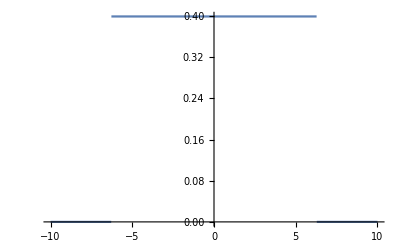

-Graphics-

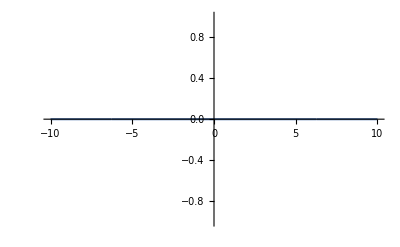

```mathematica
F=FourierTransform[2 Sinc[2 Pi t],t,ω]/.{a-> 1, b-> 0}
Plot[F,{ω,-10,10}]
Plot[Abs[F],{ω,-10,10}]
Plot[Arg[F],{ω,-10,10}]
```